### Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/botingw/code/code_test/mathematica/read_show_figs

```mathematica
FileNames[]
```

{Allexpt_config1.txt,Allexpt_corrdr_hist+1_f0_samept.pdf,Allexpt_corrdr_plotlist_samept.m,Allexpt_corrdr_xQ+1_f0_samept.pdf,Allexpt_corr_hist+1_f0_samept.pdf,Allexpt_corr_plotlist_samept.m,Allexpt_corr_xQ+1_f0_samept.pdf,Allexpt_xQbyexpt_xQ-1.m,Allexpt_xQbyexpt_xQ.pdf,CT14H2LHeC_config1.txt,H2LHeC_corrdr_plotlist_samept.m,jpnew_config1.txt,jpnew_corrdr_plotlist_samept.m,jpnew_corrdr_xQ+1_f8_samept.pdf,rename_figs_title.nb,rename_figs_title_v2.nb,test,ttbar_config1.txt,ttbar_corrdr_plotlist_samept.m,ttbar_corrdr_xQ+1_f8_samept.pdf,user_func.txt,Zpt_config1.txt,Zpt_corrdr_plotlist_samept.m,Zpt_corrdr_xQ+1_f8_samept.pdf,Zpt_dr_hist+1_samept.pdf,Zpt_dr_plotlist_samept.m}

Mathematica version-specific set up

```mathematica
Off[General::spell]
Off[General::spell1]
```

Set Interpolation Order

```mathematica
SetOptions[Interpolation,InterpolationOrder->2]
```

{InterpolationOrder→2,Method→Automatic,PeriodicInterpolation→False}

```mathematica
{InterpolationOrder->2,Method->Automatic,PeriodicInterpolation->False}
```

{InterpolationOrder→2,Method→Automatic,PeriodicInterpolation→False}

```mathematica
{InterpolationOrder->2,Method->Automatic,PeriodicInterpolation->False}
```

{InterpolationOrder→2,Method→Automatic,PeriodicInterpolation→False}

```mathematica
SetOptions[{Plot,ListPlot,Graphics,ParametricPlot},BaseStyle->{FontFamily->"Helvetica",32}];
```

### Set up the detail of the figures

```mathematica
(*
SetOptions[{Show},(*BaseStyle->{FontFamily->"Helvetica",16}*)PlotStyle->Orange];
*)
SetOptions[
{Plot,ListPlot,Graphics,ParametricPlot},
BaseStyle->{FontFamily->"Helvetica",16},
FrameTicksStyle->{{14,Black},{14,Black}},
LabelStyle->{Black}
];
```

```mathematica
titlesize=24;
```

```mathematica
Show//Options
Graphics//Options
```

{}

{AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{FontFamily→Helvetica,32},ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Method→Automatic,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{}}

```mathematica
(*figure title*)
pdfnamelable={"\!\(\*OverscriptBox[\(b\), \(_\)]\)(x,μ)","\!\(\*OverscriptBox[\(c\), \(_\)]\)(x,μ)","\!\(\*OverscriptBox[\(s\), \(_\)]\)(x,μ)","\!\(\*OverscriptBox[\(d\), \(_\)]\)(x,μ)","\!\(\*OverscriptBox[\(u\), \(_\)]\)(x,μ)","g(x,μ)","u(x,μ)","d(x,μ)","s(x,μ)","c(x,μ)","b(x,μ)"}~Join~
{"σ_H(7TeV)","σ_H(8TeV)","σ_H(14TeV)","s+(x,Q)","uval(x,Q)","dval(x,Q)","d̄/ū(x,μ)","d/u(x,μ)","g/(ū+d̄+s̄)(x,μ)","g(0.01,m_H)"}
```

{b̄(x,μ),c̄(x,μ),s̄(x,μ),d̄(x,μ),ū(x,μ),g(x,μ),u(x,μ),d(x,μ),s(x,μ),c(x,μ),b(x,μ),σ_H(7TeV),σ_H(8TeV),σ_H(14TeV),s+(x,Q),uval(x,Q),dval(x,Q),d̄/ū(x,μ),d/u(x,μ),g/(ū+d̄+s̄)(x,μ),g(0.01,m_H)}

```mathematica
title1="|S_f| for ";
title1C="|C_f| for ";
```

```mathematica
title2=pdfnamelable
```

{b̄(x,μ),c̄(x,μ),s̄(x,μ),d̄(x,μ),ū(x,μ),g(x,μ),u(x,μ),d(x,μ),s(x,μ),c(x,μ),b(x,μ),σ_H(7TeV),σ_H(8TeV),σ_H(14TeV),s+(x,Q),uval(x,Q),dval(x,Q),d̄/ū(x,μ),d/u(x,μ),g/(ū+d̄+s̄)(x,μ),g(0.01,m_H)}

### Run

#### Zpt δr hist

```mathematica
Zptdrhist=Drop[ReadList[OpenRead["Zpt_dr_plotlist_samept.m"],String ],1]//StringJoin;
```

```mathematica
Zptdrhist//Dimensions
```

{}

```mathematica
Export[
"./test/"<>"Zpt_dr_hist+1_samept.pdf",
ToExpression[StringReplace[Zptdrhist,"NNLOall"->"NNLO"] ][[3]] 
]
```

./test/Zpt_dr_hist+1_samept.pdf

#### Zpt f8 |sens| xQ

```mathematica
iflavour=8;
title3=", CT14HERA2";
title=title1<>title2[[iflavour+6]]<>title3;
```

```mathematica
pin=
Get["Zpt_corrdr_plotlist_samept.m"][[iflavour+3,1]](*,
PlotLabel->"S_f(dbar(x,Q),r_i), CT14HERA2NNLO"
*)
```

-Graphics-

```mathematica
pout=Show[
pin,
PlotLabel->Style[title,titlesize]
]
```

-Graphics-

```mathematica
Export[
"./test/"<>"Zpt_corrdr_xQ+1_f8_samept.pdf",
pout
]
```

./test/Zpt_corrdr_xQ+1_f8_samept.pdf

```mathematica
"b̄"
```

b̄

#### ttbar f8 |sens| xQ

```mathematica
iflavour=8;
title3=", CT14HERA2";
title=title1<>title2[[iflavour+6]]<>title3;
```

```mathematica
pin=
Get["ttbar_corrdr_plotlist_samept.m"][[iflavour+3,1]](*,
PlotLabel->"S_f(dbar(x,Q),r_i), CT14HERA2NNLO"
*)
```

-Graphics-

```mathematica
pout=Show[
pin,
PlotLabel->Style[title,titlesize]
]
```

-Graphics-

```mathematica
Export[
"./test/"<>"ttbar_corrdr_xQ+1_f8_samept.pdf",
pout
]
```

./test/ttbar_corrdr_xQ+1_f8_samept.pdf

#### jpnew f8 |sens| xQ

```mathematica
iflavour=8;
title3=", CT14HERA2";
title=title1<>title2[[iflavour+6]]<>title3;
```

```mathematica
pin=
Get["jpnew_corrdr_plotlist_samept.m"][[iflavour+3,1]]
```

-Graphics-

```mathematica
pout=Show[
pin,
PlotLabel->Style[title,titlesize]
]
```

-Graphics-

```mathematica
Export[
"./test/"<>"jpnew_corrdr_xQ+1_f8_samept.pdf",
pout
]
```

./test/jpnew_corrdr_xQ+1_f8_samept.pdf

#### Allexpt f0 |sens| xQ

```mathematica
iflavour=0;
title3=", CT14HERA2";
title=title1<>title2[[iflavour+6]]<>title3;
```

```mathematica
pin=
Get["Allexpt_corrdr_plotlist_samept.m"][[iflavour+3,1]]
```

-Graphics-

```mathematica
pout=Show[
pin,
PlotLabel->Style[title,titlesize]
]
```

-Graphics-

```mathematica
Export[
"./test/"<>"Allexpt_corrdr_xQ+1_f0_samept.pdf",
pout
]
```

./test/Allexpt_corrdr_xQ+1_f0_samept.pdf

#### Allexpt f0 |sens| hist

```mathematica
iflavour=0;
title3=", CT14HERA2";
title=title1<>title2[[iflavour+6]]<>title3;
```

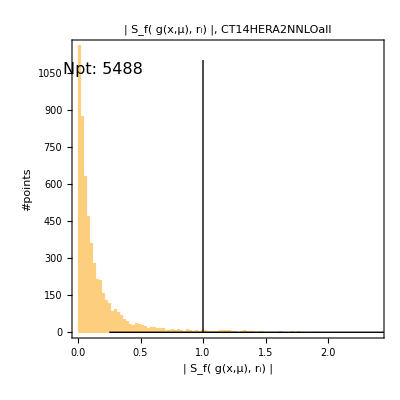

```mathematica
pin=
Get["Allexpt_corrdr_plotlist_samept.m"][[iflavour+3,3]]
```

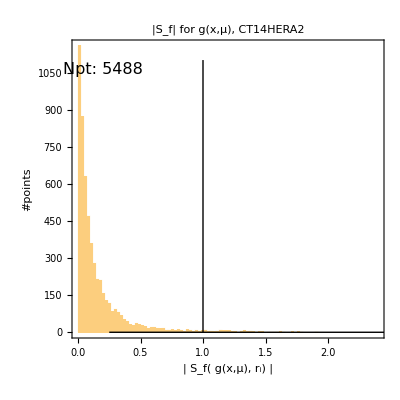

```mathematica
pout=Show[
pin,
PlotLabel->Style[title,titlesize]
]
```

```mathematica
Export[
"./test/"<>"Allexpt_corrdr_hist+1_f0_samept.pdf",
pout
]
```

./test/Allexpt_corrdr_hist+1_f0_samept.pdf

#### Allexpt f0 |corr| xQ

```mathematica
iflavour=0;
title3=", CT14HERA2";
title=title1C<>title2[[iflavour+6]]<>title3;
```

```mathematica
pin=
Get["Allexpt_corr_plotlist_samept.m"][[iflavour+3,1]]
```

-Graphics-

```mathematica
pout=Show[
pin,
PlotLabel->Style[title,titlesize]
]
```

-Graphics-

```mathematica
Export[
"./test/"<>"Allexpt_corr_xQ+1_f0_samept.pdf",
pout
]
```

./test/Allexpt_corr_xQ+1_f0_samept.pdf

#### Allexpt f0 |corr| hist

```mathematica
iflavour=0;
title3=", CT14HERA2";
title=title1C<>title2[[iflavour+6]]<>title3;
```

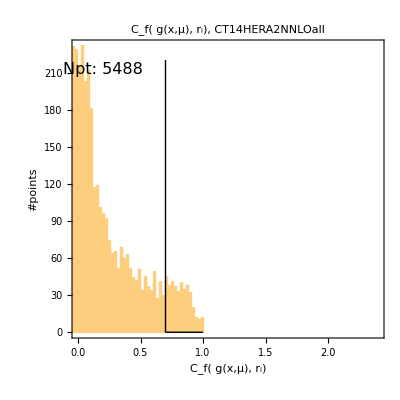

```mathematica
pin=
Get["Allexpt_corr_plotlist_samept.m"][[iflavour+3,3]]
```

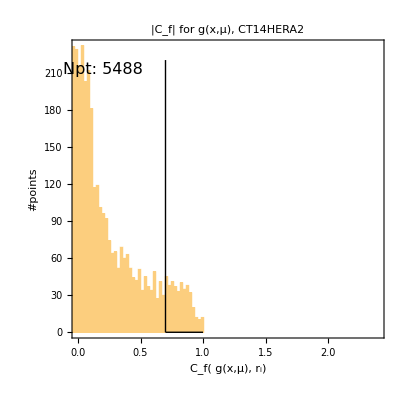

```mathematica
pout=Show[
pin,
PlotLabel->Style[title,titlesize]
]
```

```mathematica
Export[
"./test/"<>"Allexpt_corr_hist+1_f0_samept.pdf",
pout
]
```

./test/Allexpt_corr_hist+1_f0_samept.pdf

#### xQ plot by expt id

```mathematica
title="Experimental data in CT14HERA2 analysis"
```

Experimental data in CT14HERA2 analysis

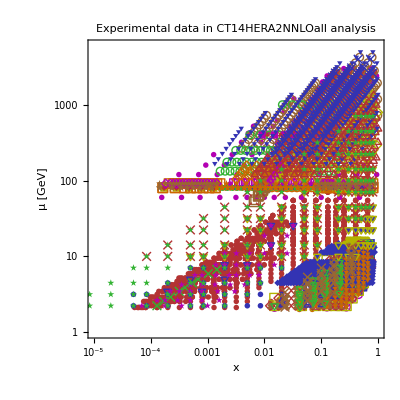

```mathematica
pin=
Get["Allexpt_xQbyexpt_xQ-1.m"]
```

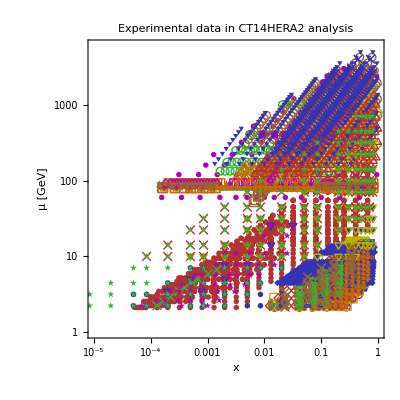

```mathematica
pout=Show[
pin,
PlotLabel->Style[title,titlesize]
]
```

```mathematica
Export[
"./test/"<>"Allexpt_xQbyexpt_xQ.pdf",
pout
]
```

./test/Allexpt_xQbyexpt_xQ.pdf

#### CT14HERA2 LHeC g |sens| xQ

```mathematica
iflavour=0;
title3=", CT14HERA2";
title=title1<>title2[[iflavour+6]]<>title3;
```

```mathematica
pin=
Get["H2LHeC_corrdr_plotlist_samept.m"][[iflavour+3,1]]
```

-Graphics-

```mathematica
pout=Show[
pin,
PlotLabel->Style[title,titlesize]
]
```

-Graphics-

```mathematica
Export[
"./test/"<>"H2LHeC_corrdr_xQ+1_f0_samept.pdf",
pout
]
```

./test/H2LHeC_corrdr_xQ+1_f0_samept.pdf

#### CT14HERA2 LHeC d |sens| xQ

```mathematica
iflavour=2;
title3=", CT14HERA2";
title=title1<>title2[[iflavour+6]]<>title3;
```

```mathematica
pin=
Get["H2LHeC_corrdr_plotlist_samept.m"][[iflavour+3,1]]
```

-Graphics-

```mathematica
pout=Show[
pin,
PlotLabel->Style[title,titlesize]
]
```

-Graphics-

```mathematica
Export[
"./test/"<>"H2LHeC_corrdr_xQ+1_f2_samept.pdf",
pout
]
```

./test/H2LHeC_corrdr_xQ+1_f2_samept.pdf